```mathematica
<<MaTeX`
```

MaTeX::shdw: Symbol MaTeX appears in multiple contexts {MaTeX`,Global`}; definitions in context MaTeX` may shadow or be shadowed by other definitions.

```mathematica
Transpose[{epsilon,fidelity}]
```

{{0.,1.},{0.01,0.696298},{0.02,0.514565},{0.03,0.40621},{0.04,0.341851},{0.05,0.303774},{0.06,0.28134},{0.07,0.268179},{0.08,0.260493},{0.09,0.256025},{0.1,0.253441},{0.11,0.251954},{0.12,0.251104},{0.13,0.250619},{0.14,0.250345},{0.15,0.250191},{0.16,0.250105},{0.17,0.250057},{0.18,0.250031},{0.19,0.250017},{0.2,0.250009}}

```mathematica
Transpose[{epsilon,purifiedN1Noisy}]
```

{{0.,1.},{0.01,0.99049015932828cd 31},{0.02,0.980243},{0.03,0.969258},{0.04,0.957538},{0.05,0.945097},{0.06,0.931956},{0.07,0.918144},{0.08,0.903698},{0.09,0.888663},{0.1,0.873092},{0.11,0.857042},{0.12,0.840577},{0.13,0.823767},{0.14,0.806681},{0.15,0.789393},{0.16,0.771975},{0.17,0.754499},{0.18,0.737036},{0.19,0.719652},{0.2,0.702409}}

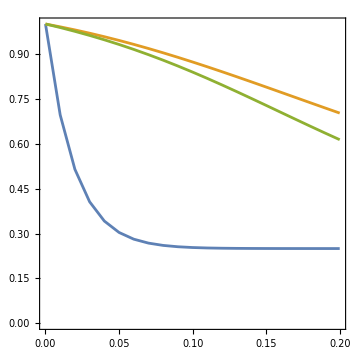

```mathematica
(*Import data from CSV*)data=Import[NotebookDirectory[]<>"data_output.csv","CSV"];

(*Extract individual columns*)
epsilon=data[[2;;,1]];
fidelity=data[[2;;,2]];
purifiedN1Noisy=data[[2;;,3]];
purifiedN2Noisy=data[[2;;,4]];

(*Generate the plot*)
ListLinePlot[{Transpose[{epsilon,fidelity}],Transpose[{epsilon,purifiedN1Noisy}],Transpose[{epsilon,purifiedN2Noisy}]},

AspectRatio->1,PlotLegends->Placed[LineLegend[{MaTeX["\\text{Non-Purified}",FontSize->15],MaTeX["\\text{SWAPNET12-13 } n=1",FontSize->15],MaTeX["\\text{SWAPNET12-13 } n=2",FontSize->15]},Background->White,LegendFunction->"Frame",FrameStyle->Gray],{Right,Top}],Background->White,Frame->True,FrameLabel->{MaTeX["\\epsilon \\text{ (Noise Parameter)}",FontSize->15],MaTeX["\\mathcal{F} \\text{ (Fidelity)}",FontSize->15]},BaseStyle->{FontFamily->"CMU Serif",FontSize->12},FrameTicks->Automatic,ImageSize->Medium]
```